# Lagrange Triangle Shape Functions

This document derives Lagrange interpolation formulas for triangles up to degree 4 and also computes the weights for evaluating the integrals of these interpolants.

Linear Triangle

Linear functions on triangles can be uniquely defined by specifying their values at the triangle corners; the linear shape functions then produce the linear function by interpolating these corner values. The linear shape function for a corner is the unique linear function assuming value 1 at that corner and 0 at the rest.

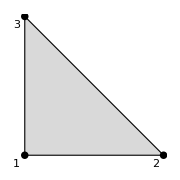

```mathematica
linearNodes={{0,0},{1,0},{0,1}};
triNodesIcon[valueNodes_,slopeNodes_:{}]:=Graphics[{FaceForm[LightGray],EdgeForm[Black],Thick,PointSize[0.03],Triangle[linearNodes],
MapIndexed[{Point[#1],Text[#2[[1]],#1-{.06,.06}]}&,valueNodes],Circle[#,0.04]&/@slopeNodes},ImageSize->Small]
triNodesIcon[linearNodes]
```

We define the linear shape functions (and all other shape functions in this document) in the “canonical” coordinate system (ξ,η) where the triangle corners are (0, 0), (1, 0), and (0, 1). To evaluate the linear shape functions on an arbitrary triangle in (x, y, z) space, we first transform the triangle into this canonical coordinate system.

```mathematica
barycentricCoordinates[ξ_,η_]:={1-ξ-η,ξ,η}
linearShapeFunction[n_,ξ_,η_]:=barycentricCoordinates[ξ,η][[n]]
```

```mathematica
plotTriFunc[f_]:=Plot3D[f[ξ,η],{ξ,0,1},{η,0,1},RegionFunction->Function[{ξ,η},ξ+η≤1],PlotRange->Full]
GraphicsGrid[{Table[plotTriFunc[linearShapeFunction[n,#1,#2]&],{n,1,3}]},ImageSize->Full]
```

-Graphics-

Quadratic Lagrange Triangle

Quadratic functions on triangles can be uniquely defined by specifying their values at corner and edge midpoint nodes. The quadratic function interpolating these nodal values is expressed most simply as a linear combination of the Lagrange polynomial shape functions using the node values as coefficients. These Lagrange polynomials are defined by the constraint that they assume value 1 at a single node and 0 at all the rest.
As an aside, we note that while these shape functions are “complete” for the plate bending equations (they represent all polynomials of degree ≤ 2 exactly), they experience bad slope discontinuities because only function values, not derivative values, are shared with neighboring elements--in contrast to the cubic Hermite triangle below.

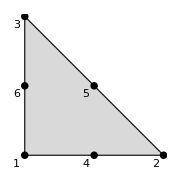

```mathematica
quadraticNodes=Join[linearNodes,{{1/2,0},{1/2,1/2},{0,1/2}}];
triNodesIcon[quadraticNodes]
```

```mathematica
edgeEndpoints[n_]:={n - 3,Mod[n - 2,3,1]}
```

The quadratic shape functions at the corners need to vanish where their corresponding linear shape function (“barycentric coordinate”) equals 0 or 1/2 (this defines two straight lines passing through all other nodes). The edge shape functions need to vanish when the linear shape function corresponding to either of its edge endpoint vertices vanishes (i.e., along both of the other edges). In both cases, these conditions define the roots of the shape function polynomial, and we can build the shape functions by taking a product of two factors. We also need to normalize these shape functions so that they evaluate to 1 at their corresponding node.

```mathematica
quadraticShapeFunction[n_,ξ_,η_]:=With[{λ=barycentricCoordinates[ξ,η]},If[n<4,2λ[[n]](λ[[n]]-1/2),4Times@@λ[[edgeEndpoints[n]]]]]
```

```mathematica
GraphicsGrid[ArrayReshape[Table[plotTriFunc[quadraticShapeFunction[n,#1,#2]&],{n,1,6}],{2,3}],ImageSize->Full]
```

-Graphics-

Cubic Lagrange Triangle

Cubic functions on triangles have 10 degrees of freedom (one per cubic monomial). We position the 10 nodes as follows:

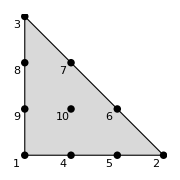

```mathematica
cubicNodes=Join[linearNodes,{{1/3,0},{2/3,0},{2/3,1/3},{1/3,2/3},{0,2/3},{0,1/3},{1/3,1/3}}];
triNodesIcon[cubicNodes]
```

Again, the Lagrange shape function for a node is defined to assume value 1 at the node and vanish at all others. We determine this shape function by finding lines of constant barycentric coordinates passing through all other nodes. E.g., for corner node i, these are the diagonals λ_i=0,1/3,2/3.

```mathematica
cubicShapeFunction[n_,ξ_,η_]:=With[{λ=barycentricCoordinates[ξ,η]},If[n<4,
(*Corner nodes*)9/2 Times@@(λ[[n]]-{0,1/3,2/3}),
If[n<10,(*Edge nodes*)27/2 With[{edge= Floor[(n - 2)/2]}, λ[[edge]]λ[[Mod[edge + 1,3,1]]](λ[[If[OddQ[n],Mod[edge+1,3,1],edge]]]-1/3)],
(*Center node*)27 Times@@λ]]]
```

```mathematica
Simplify[Dot[Table[cubicShapeFunction[n,η,ξ],{n,1,10}],#1 + 2#2 &@@@ cubicNodes]]
```

η+2 ξ

```mathematica
GraphicsGrid[Partition[Table[plotTriFunc[cubicShapeFunction[n,#1,#2]&],{n,1,10}],UpTo[3]],ImageSize->Full]
```

-Graphics-

Quartic Lagrange Triangle

Quartic functions on triangles have 15 degrees of freedom.

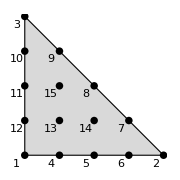

```mathematica
quarticNodes=Join[linearNodes,{{1/4,0},{2/4,0},{3/4,0},
{3/4,1/4},{2/4,2/4},{1/4,3/4},
{0,3/4},{0,2/4},{0,1/4},
{1/4,1/4},{2/4,1/4},{1/4,2/4}}];
triNodesIcon[quarticNodes]
```

```mathematica
quarticShapeFunction[n_,ξ_,η_]:=With[{λ=barycentricCoordinates[ξ,η]},If[n<4,
(*Corner nodes*)32/3 Times@@(λ[[n]]-{0,1/4,2/4,3/4}),
If[n<13,(*Edge nodes*)
With[{e1= Floor[(n - 4)/3]+1,e2=Mod[Floor[(n - 4)/3]+2,3,1]},
Switch[Mod[n-4,3],
0,128/3 λ[[e1]](λ[[e1]]-1/4)(λ[[e1]]-2/4)λ[[e2]],
1,   64λ[[e1]](λ[[e1]]-1/4)(λ[[e2]]-1/4)λ[[e2]],
2,128/3 λ[[e1]](λ[[e2]]-2/4)(λ[[e2]]-1/4)λ[[e2]]]],
(*Central nodes*)128(Times@@λ)(λ[[n-12]] - 1/4)]]]
```

```mathematica
Table[quarticShapeFunction[n,#1,#2]&@@@quarticNodes,{n,1,15}]==IdentityMatrix[15]
```

True

```mathematica
Simplify[Total[Table[quarticShapeFunction[n,ξ,η],{n,1,15}]]]
```

1

```mathematica
GraphicsGrid[Partition[Table[plotTriFunc[quarticShapeFunction[n,#1,#2]&],{n,1,15}],UpTo[3]],ImageSize->Full]
```

-Graphics-

## Shape function integrals

By integrating each shape function over the triangle, we can get weights for evaluating integrals of any interpolant. We scale the integral so that it corresponds to a triangle of area 1 (as opposed to the canonical triangle’s area of 1/2).

```mathematica
intTriFunc[f_]:=2∫_0^1 ∫_0^(1-ξ) f[ξ,η]ⅆηⅆξ
```

```mathematica
Table[intTriFunc[linearShapeFunction[n,#1,#2]&],{n,1,3}]
```

{1/3,1/3,1/3}

```mathematica
Table[intTriFunc[quadraticShapeFunction[n,#1,#2]&],{n,1,6}]
```

{0,0,0,1/3,1/3,1/3}

```mathematica
Table[intTriFunc[cubicShapeFunction[n,#1,#2]&],{n,1,10}]
```

{1/30,1/30,1/30,3/40,3/40,3/40,3/40,3/40,3/40,9/20}

```mathematica
Table[intTriFunc[quarticShapeFunction[n,#1,#2]&],{n,1,15}]
```

{0,0,0,4/45,-1/45,4/45,4/45,-1/45,4/45,4/45,-1/45,4/45,8/45,8/45,8/45}